# Vaje za 2. teden

7. 3. 2024

## Ponovitev

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato pa še tako, da definiraš vrednost spremenljivke x.
Spremenljivko x na koncu pobriši.

```mathematica
1 + x + x^2 + x^3 /. x -> 1/(Sqrt[E] + 1)/Sqrt[Pi]
```

1+1/((1+√ⅇ)^3 π^(3/2))+1/((1+√ⅇ)^2 π)+1/((1+√ⅇ) √π)

```mathematica
% // N
```

1.26804

## Naloga 1

Izračunaj 1000-i decimalki števil e in π na dva načina:
1. Tako da izračunaš dovolj decimalk obeh števil in pogledaš ustrezno decimalko pri koncu. Zakaj zadnja decimalka ne bo v redu? Uporabi funkcijo N tako, da ji podaš natančnost.
2. Z uporabo funkcije RealDigits in izpisom ustreznega elementa seznama.

Določi še 5., 100. in 443. decimalko.

Napiši fuknkcijo, ki sprejme poljubno realno število x in naravno število n in vrne n-to decimalko števila x.

```mathematica
N[E, 1002]
N[Pi, 1002]
```

2.7182818284590452353602874713526624977572470936999595749669676277240766303535475945713821785251664274274663919320030599218174135966290435729003342952605956307381323286279434907632338298807531952510190115738341879307021540891499348841675092447614606680822648001684774118537423454424371075390777449920695517027618386062613313845830007520449338265602976067371132007093287091274437470472306969772093101416928368190255151086574637721112523897844250569536967707854499699679468644549059879316368892300987931277361782154249992295763514822082698951936680331825288693984964651058209392398294887933203625094431173012381970684161403970198376793206832823764648042953118023287825098194558153017567173613320698112509961818815930416903515988885193458072738667385894228792284998920868058257492796104841984443634632449684875602336248270419786232090021609902353043699418491463140934317381436405462531520961836908887070167683964243781405927145635490613031072085103837505101157477041718986106873969655212671546889570350354

3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534211706798214808651328230664709384460955058223172535940812848111745028410270193852110555964462294895493038196442881097566593344612847564823378678316527120190914564856692346034861045432664821339360726024914127372458700660631558817488152092096282925409171536436789259036001133053054882046652138414695194151160943305727036575959195309218611738193261179310511854807446237996274956735188575272489122793818301194912983367336244065664308602139494639522473719070217986094370277053921717629317675238467481846766940513200056812714526356082778577134275778960917363717872146844090122495343014654958537105079227968925892354201995611212902196086403441815981362977477130996051870721134999999837297804995105973173281609631859502445945534690830264252230825334468503526193118817101000313783875288658753320838142061717766914730359825349042875546873115956286388235378759375195778185778053217122680661300192787661119590921642019894

```mathematica
f[x_, n_] := Last[RealDigits[x, 10, n + Ceiling[Log[10, x]]][[1]]];
```

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše spodnji niz, kjer naj bo niz “___” nadomeščen s pravim rezultatom.
"Vsota sin(π/8) + cos(π/8) je enaka ___."

```mathematica
izraz = Sin[Pi/8] + Cos[Pi/8];
posenostavljenIzraz = Sin[Pi /8] + Cos[Pi/8] // FullSimplify;
```

```mathematica
niz = StringForm["Vsota sin() + cos() je enaka ``.", posenostavljenIzraz]
```

Vsota sin() + cos() je enaka √(1+1/(√2)).

## Naloga 3

Napiši  funkcijo poenostaviInIzpisi, ki  bo  sprejela  izraz “izr”, ga  poenostavila  in  rezultat  izpisala  v  obliki
“Izraz [izr] se poenostavi v izraz [poenostavljen_izraz]”,
kjer je [izr] nadomestite z vnešenim izrazom, [poenostavljen_izraz] pa s poenostavljenim izrazom.

```mathematica
poenostaviInIzpisi[izr_] := TemplateApply[
StringTemplate["Izraz `izr` se poenostavi v izraz `poenostavljen_izr`"], 
<|
"izr" -> ToString[izr, StandardForm],
"poenostavljen_izr" -> ToString[izr // FullSimplify, StandardForm]
|>]
```

```mathematica
poenostaviInIzpisi[Sin[Pi/8] + Cos[Pi/8]]
```

Izraz Cos[π/8]+Sin[π/8] se poenostavi v izraz √(1+1/(√2))

## Naloga 4

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?
Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:
“Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.”
Pomagaj si z vodičem za generiranje nizov (predvsem del za vstavljanje izrazov) in uporabi funkcijo TemplateApply, da definiraš zgornji niz še brez direktnega vnašanja števila 668.

```mathematica
niz = TemplateApply["Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = <* 249 + 419 *> jabolk."];
```

```mathematica
niz
```

Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.

## Naloga 5

1. Definiraj funkcijo f(x)=x^2+3x+2+sin(x).
2. Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).
3. Nariši graf funkcije f na intervalu [-10,10].
4. Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot anonimno funkcijo s formalnim parametrom #.
5. Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot anonimno funkcijo.

```mathematica
f[x_] := x^2 + 3x + 2 + Sin[x];
f[3] + f[4] // N;
```

```mathematica
(3 //f) + (4 //f) //N;
```

```mathematica
Plot[f[x], {x, -10, 10}];
```

```mathematica
g = #^2 + 3#+2+Sin[#] &;
```

```mathematica
h[x_, y_] := (f[x] + g[y])^2;
```

```mathematica
h = Power[f[#1] + g[#2], 2]&;
```

## Naloga 6

1. Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.
2. Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.
3. Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

```mathematica
Clear[f, g];
f[x_] := x^3 + x + 1;
g[n_] := Mod[n, 7];
```

```mathematica
f /@ Range[100];
t = Table[f[x], {x, 1, 100}];
Select[t, g[#] == 3 &];
```

```mathematica
Select[Table[x^3 +  x+ 1 , {x, 1, 100}], Mod[#, 7] == 3 &];
```

## Naloga 7

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y]
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4]
```

25

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode z uporabo anonimne funkcije, ki vsebuje le 1 vrstico.

```mathematica
(#1[#2, #3]&)[#1^2 + #2^2&, 3, 4];
```

## Naloga 8

Nariši graf funkcije f (x, y, z) = x  sin (xy)  cos (xy + z), kjer za z-koordinato uporabi  slider.

```mathematica
f[x_, y_, z_] := x * Sin[x*y] * Cos[x*y+z];
Manipulate[Plot3D[f[x,y,z], {x, -10, 10}, {y, -10, 10}], {z, -10, 10}]
```

## Naloga 9

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Pomagaj si s funkcijo Graphics. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

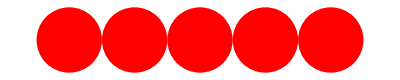

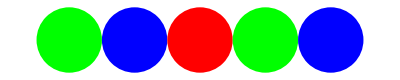
Za dodatni izziv poskusi napisati funkcijo MesaniKrogi[n], ki bo narisala kroge v izmenjajočih barvah. Na primer:
-Graphics-

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti).

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato.

-Graphics3D-

```mathematica
DvojniSeznam[n_]:= Join[Range[n], Range[n]];
```

```mathematica
Krogi[n_] := Table[Disk[{2 i, 0}], {i, n}];
NarisiKroge[n_] :=Graphics[Join[{Red}, Krogi[n]]];
MesaniKrogiBarve[n_] := If[
Mod[n, 3] == 0,
{Red, Disk[{2n, 0}]}, 
If[Mod[n, 3] == 1, 
{Green, Disk[{2n, 0}]},
{Blue, Disk[{2n, 0}]},
]];
MesaniKrogi[n_] := Graphics[MesaniKrogiBarve /@ Range[n]];
```

```mathematica
Krogi3D[n_] := Table[Sphere[{2i, 0, 0}], {i,n}];
Narisi3DKroge[n_] := Graphics3D[Krogi3D[n]];
Manipulate[Graphics3D[{Sphere[{0,v1,0}, 0.1], Sphere[{0.2, v2,0}, 0.1], Sphere[{0.4,v3,0}, 0.1]}], {v1, 0, 1}, {v2, 0, 1}, {v3, 0, 1}]
```

## Naloga 10

Napiši funkcijo, ki sprejme narvni števili m in n in vrne seznam prvih n členov Collatzovega zaporedja za število m. Pomagaj si s funkcijo “RecurrenceTable”.

```mathematica
Clear[f, k];
g[m_, n_]:= RecurrenceTable[f[k + 1]==If[Mod[f[k], 2] == 0, Floor[f[k] / 2], 3 f[k]+ 1] && f[1] == m,f,{k,1,n}]
```

```mathematica
g[12, 10]
```

{12,6,3,10,5,16,8,4,2,1}